```mathematica
n=50;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,100}]];
AdjacencyGraph[k]*)
```

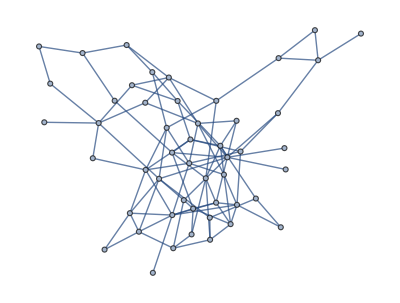
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<200>, {50, 50}]

```mathematica
data={-2.011965405172883,2.335459383504287,1.9515759438820186,-1.50918233099809,0.36500058212146264,-0.9486410950850714,-2.267517547555653,2.1728271671818256,1.3395924618960569,1.7673621167409954,0.4934843684967091,1.008928693550258,2.919356489986493,0.3506681711002626,3.0565981067613928,0.8867063046741093,-0.23883331870730842,-2.885430820114126,1.6051992639389034,0.9102491907625306,1.695748489844637,-2.9300347925407104,1.032188182006008,-2.5750500599055672,1.107985244131974,0.45786004035142364,1.018730664383935,-0.6552072681638988,-2.1163628147605547,2.8718766176896544,-1.6580877313704294,-2.9598636930343334,-0.43971741798382,2.7783931983894883,3.099332098076033,0.3413205119544065,0.7980075465626111,1.4805959739801984,2.945143988501039,-3.0327887744943784,-0.8118091987294499,-2.3833779223204092,1.8532401557221163,2.5876742753160746,2.883452449662921,1.384443522896243,-2.929260090600146,-1.0721445056510215,-2.3102727050459997,2.6569893986533932};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,0],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==6-3/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}]
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}]
ukupfrust[5000]
data2=Flatten[Table[Mod[Subscript[z,i][tt],2Pi],{i,1,n}]]
```

{-0.161067,-0.0521055,-0.0127254,-0.0642459,-0.0230649,-0.14346,-0.0330305,-0.286719,-0.311348,-0.620896,-0.0117843,-0.0114171,-0.0250556,-0.00179039,-0.0560499,-0.00375964,-0.113551,-0.0946881,-0.0000177693,-0.000689676,-0.0683888,-0.270108,-0.231961,-0.427319,-0.11635,-0.0737088,-0.0372333,-0.0501247,-0.0154372,-0.0078275,-0.00441399,-0.0331322,-0.125042,-0.0419513,-0.241559,-0.0906315,-0.210488,-0.36155,-0.390111,-0.0105688,-0.0683861,-0.0640159,-0.00817458,-0.051656,-0.174484,-0.0403308,-0.0626054,-0.0185474,-0.146488}

{14.4038}

{1.14001,3.96841,3.90285,5.97388,3.67555,1.42673,5.085,2.35897,1.10698,3.01627,2.58238,2.46507,3.97624,2.74617,5.48568,3.98065,0.863484,5.62626,2.46883,2.67778,0.96352,5.67792,2.37076,5.95534,2.40902,3.24823,3.95297,0.876209,5.61809,4.01378,0.650312,4.18078,2.38217,5.89273,0.811379,2.67709,2.40723,2.67707,5.55407,5.8524,1.73808,6.12037,3.86561,4.72345,4.51297,3.7919,4.13882,0.940455,5.47511,4.42233}

```mathematica
zvuk={1,3,3,4,3,1,4,2,1,3,2,2,3,2,4,3,1,4,2,2,1,4,2,4,2,3,3,1,4,4,1,4,2,4,1,2,2,2,4,4,1,4,3,4,4,3,4,1,4,4};
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];
Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];
findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
a=Table[findAllRoots[Sin[(Subscript[z,i][t])/2],{t,0,60}],{i,1,n}];
```

```mathematica
Sound[Flatten[Table[Table[If[Round[a[[i]][[j]],0.04]==t,If[zvuk[[i]]==1,SoundNote["G",{t,t+0.1},"Banjo"],If[zvuk[[i]]==2,SoundNote["B",{t,t+0.1},"Banjo"],If[zvuk[[i]]==3,SoundNote["D",{t,t+0.1},"Banjo"],SoundNote["F",{t,t+0.1},"Banjo"]]]],SoundNote[None,{t,t+0.1}]],{i,1,n},{j,1,Length[a[[i]]]}],{t,0,60,0.04}]],{0,150.1}]
```

```mathematica
Export["sim7_banjo.mp3",%29]
```

sim7_banjo.mp3

```mathematica
Export["SM7.mid",%29]
```

SM7.mid

```mathematica
granica=60;
```

```mathematica
video[t_]:=Grid[{{GraphPlot[SomeGraph,PlotStyle->{Gray,Thickness[0.004]},VertexRenderingFunction->({Hue[Rescale[lisboj[t][[Sequence@@#2]],{0,2Pi}]],Disk[#1,0.12]}&),ImageSize->700,PlotRangePadding->0],Show[{With[{sectors=360},angle=2 Pi/sectors;
Graphics[{Table[{Hue[i/sectors],EdgeForm[{Thick,Hue[i/sectors]}],Disk[{0,0},1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]],ListPlot[{Re[#],Im[#]}&/@data1[t],PlotStyle->Directive[Black,PointSize[.025]]],ListPlot[{0,1},PlotStyle->Directive[Gray,PointSize[.025]]]},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],Axes->True,AxesOrigin->{0,0},PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImagePadding->40,AspectRatio->1],Show[{Plot[ukupfrust[tt],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

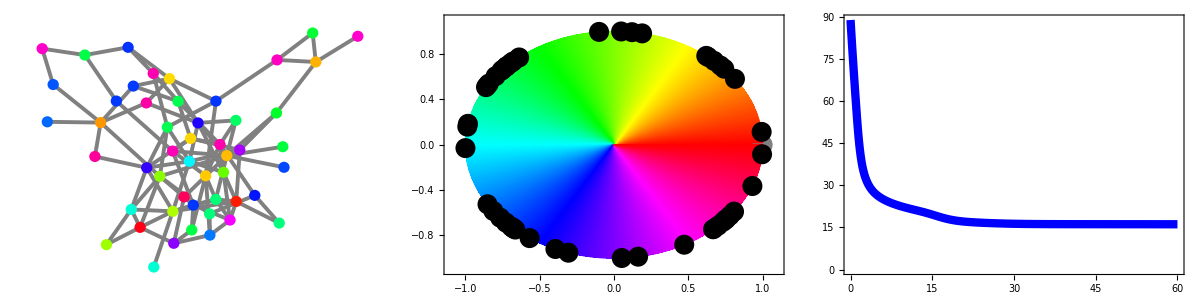

```mathematica
video[60]
```

```mathematica
simulaci1=Table[video[t],{t,0,60,0.04}];
```

```mathematica
Export["SM7.AVI",simulaci1]
```